# Forced precession under the far-field torques

## 1. Without near-field torques

```mathematica
yr=31557600.0;
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
linearspace[a_,b_,n_]:=N[Range[a,b,(b-a)/n]];
logspace[a_,b_,n_]:=N[10^Range[a,b,(b-a)/n]];
farfield[ϵ_,δ_,P_,B_,k_,M_,R_,χ_,η_,θ_,k1_,k2_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;I0=2/5*M*R^2;
ϵ1=(δ ϵ)/(1+δ+ϵ);
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t])+1/(I0 c^3)k1 ω0  (u1[t]^2+u2[t]^2+u3[t]^2)  (-k2 ω0 u1[t] m^2+m^2 ω0 Cos[η] Sin[χ] (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t])),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1)+1/((1+ϵ1)I0 c^3)k1 ω0 (u1[t]^2+u2[t]^2+u3[t]^2) (-k2 ω0 u2[t] m^2+m^2 ω0 Sin[η] Sin[χ] (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t])), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ)+ (u1[t]^2+u2[t]^2+u3[t]^2)/((1+ϵ)I0*c^3)k1 ω0  (-k2 ω0 u3[t] m^2+m^2 ω0 Cos[χ] (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t])),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,10*yr},Method->"ExplicitRungeKutta",InterpolationOrder->All]
; sol]
Spindown1[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
N0=(k1 μ^2*ω0^2)/(c^3 I0);
τ=ωp*t;

l1=-N0*k2*t;
l2=N0/ωp*(EllipticE[JacobiAmplitude[τ,m],m] (μ3^2 Cos[θ0]^2+((μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/m)+(((-1+m) μ1^2+(1+δ) μ2^2) τ Sin[θ0]^2)/m-(2 √(1+δ) μ1 μ2 JacobiDN[τ,m] Sin[θ0]^2)/m+μ1 μ3 JacobiSN[τ,m] Sin[2 θ0]-√(1+δ) μ2 μ3 JacobiCN[τ,m] Sin[2 θ0]+1/m(2 √(1+δ) μ1 μ2 Sin[θ0]^2+m √(1+δ) μ2 μ3 Sin[2 θ0]));
l=l1+l2;
l

]
```

## Consistency of the numerical and analytical solutions

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

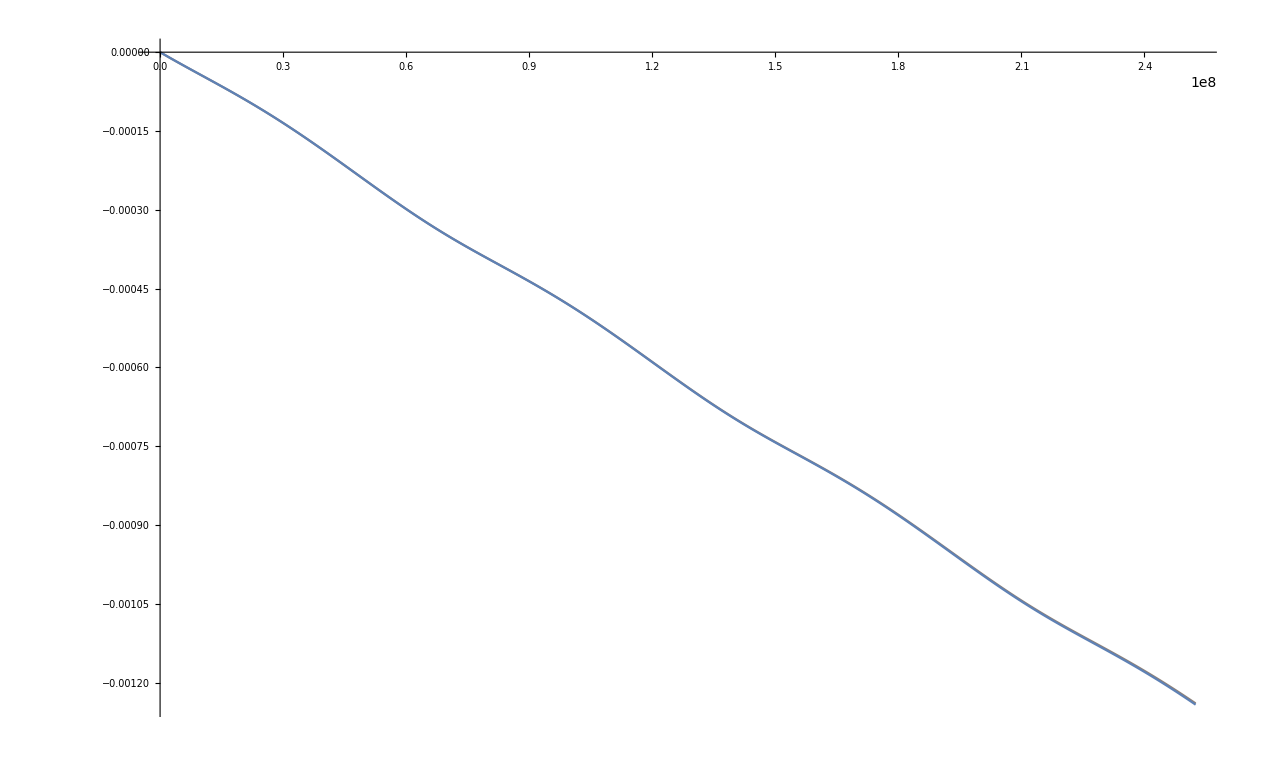

```mathematica
ϵ=10^-7;
δ=1;
P=5;
ω0=2*π/P;
B=5*10^14;
k=0.0;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=10/180.0*π;
k1=1;
k2=2;
sol=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[ϵ,δ,P,B,k,M,R,χ,η,θ,k1,k2]]]
time=linearspace[0,8*yr,600];
re=(sol/.t-> time);
time=linearspace[0,8*yr,600];
list1=ListPlot[Transpose@{time,(re[[1]]^2+re[[2]]^2+re[[3]]^2)^0.5-1},ColorFunction->"Rainbow",Joined->True];
list2=ListPlot[Transpose@{time,Spindown1[ϵ,δ,χ,η,θ,B,P,k1,k2,time]},Joined->True];
Show[list1,list2,Background-> White]
```

## The special biaxial case

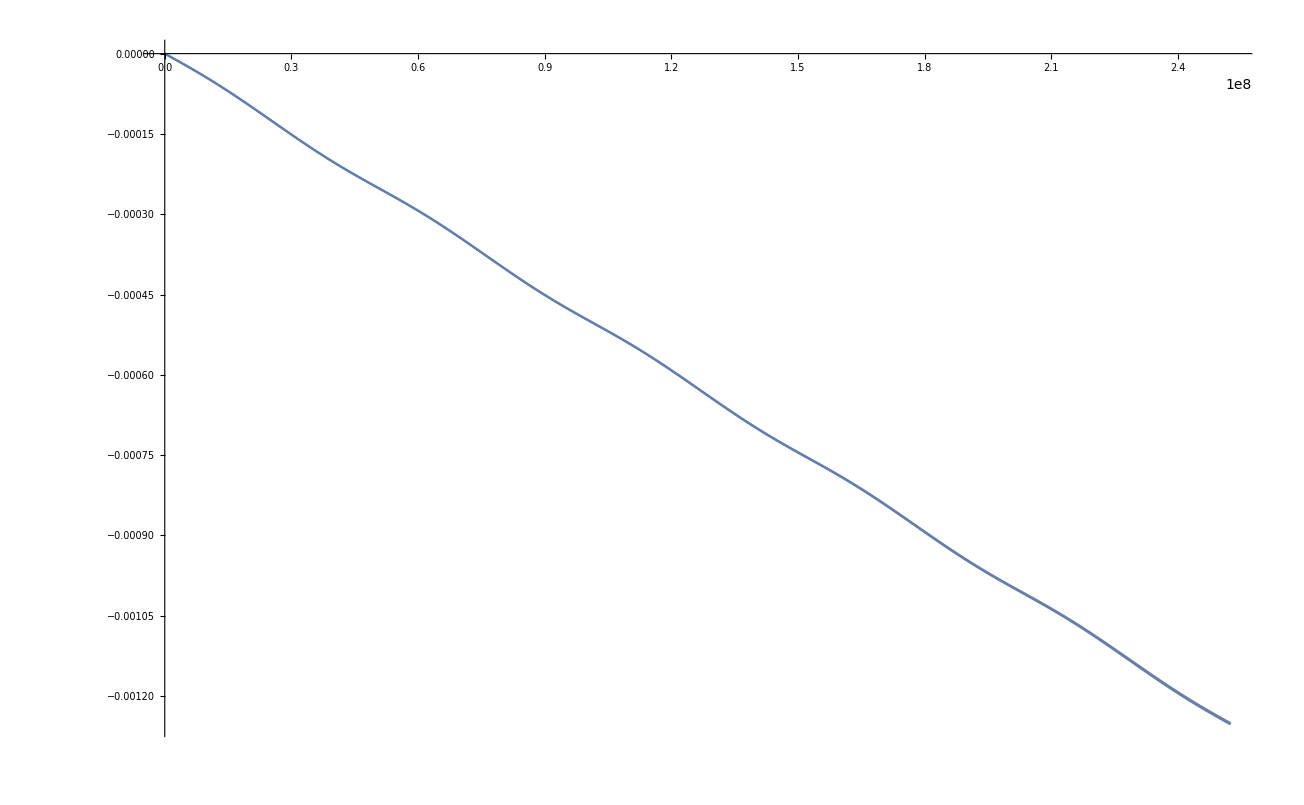

```mathematica
ϵ=10^-7;
δ=0;
P=5;
B=5*10^14;
k=0.0;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=0.0/180*π;
θ=10/180.0*π;
k1=1;
k2=2;
Spindown2[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=(I1^2*ω0^2*Sin[θ0]^2+I3^2*ω0^2*Cos[θ0]^2)^0.5;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
(*L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];*)
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=-N0*k2*t;
τ=ωp*t;
l2=N0/ωp*(1/4 (μ1^2 τ+2 μ3^2 τ-(μ1^2-2 μ3^2) τ Cos[2 θ0]+8 μ1 μ3 Cos[θ0] Sin[θ0] Sin[τ]+μ1^2 Sin[θ0]^2 Sin[2 τ]));
l=l1+l2;
l

]
sol=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[ϵ,δ,P,B,k,M,R,χ,η,θ,k1,k2]]];
re=sol/.t-> time;
list1=ListPlot[Transpose@{time,(re[[1]]^2+re[[2]]^2+re[[3]]^2)^0.5-1},Joined->True,ColorFunction->Hue];
list2=ListPlot[Transpose@{time,Spindown2[ϵ,δ,χ,η,θ,B,P,k1,k2,time]},Joined->True];
Show[list1,list2,Background-> White]
```

## Consider the near-field torque

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

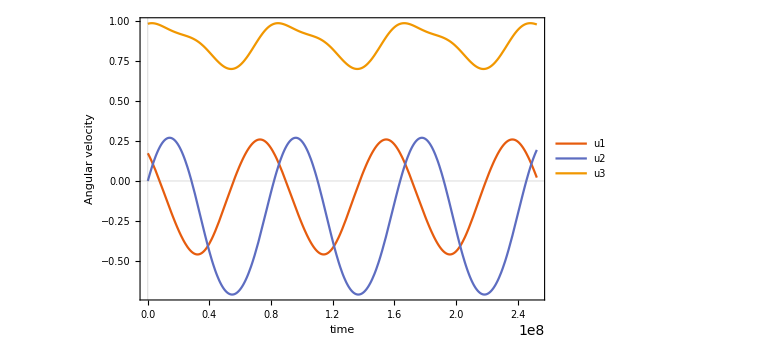

```mathematica
near[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;I0=2/5*M*R^2;
ϵ1=(δ ϵ)/(1+δ+ϵ);
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,10*yr},Method->"ExplicitRungeKutta"]
; sol];

ϵ=10^-7;
δ=1;
P=5;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=10/180.0*π;
sol=Evaluate[near[ϵ,δ,χ,η,θ,B,P,k]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,8*yr},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

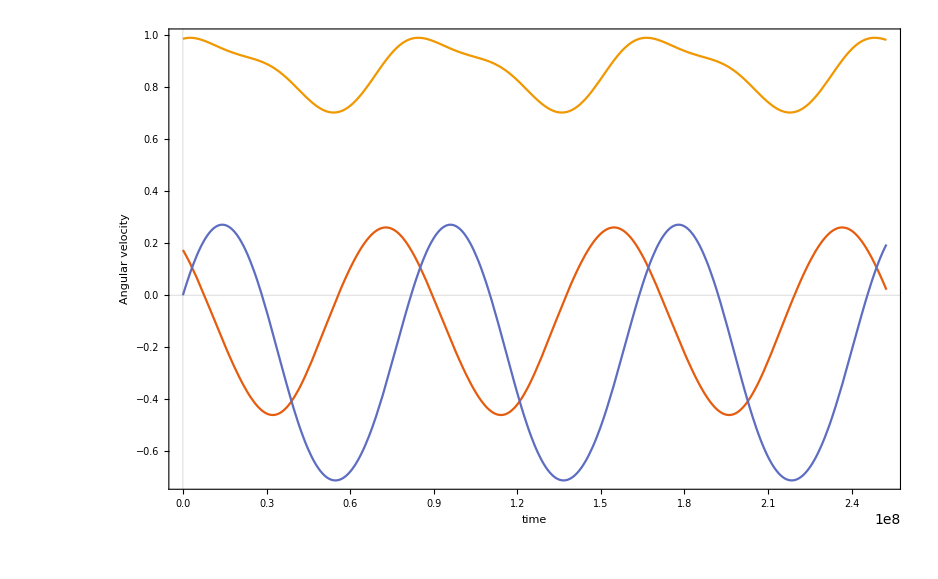

```mathematica
effective[ϵ_,δ_,P_,B_,k_,M_,R_,χ_,η_,θ_,t_]:=Module[{sol},
ϵ1=(δ ϵ)/(1+δ+ϵ);
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);

h=UnitStep[Ltol^2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e1)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e1)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e1),Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e2)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e2)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e2),Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e3)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e3)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e3)},h==0,sol={0,0,0}];{sol}];
Plot[{Evaluate[effective[ϵ,δ,P,B,k,M,R,χ,η,θ,t]]},{t,0,8*yr},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]
```

## Analytical integration

```mathematica
Remove["Global`*"]
cosα=μ1*Sin[θ0]*JacobiCN[τ,m]+μ2*Sin[θ0]*(1+δ)^(1/2)JacobiSN[τ,m]+μ3*Cos[θ0]*JacobiDN[τ,m]
core=Expand[cosα^2]
```

Remove::rmnsm: There are no symbols matching "Global`*".

μ3 Cos[θ0] JacobiDN[τ,m]+μ1 JacobiCN[τ,m] Sin[θ0]+√(1+δ) μ2 JacobiSN[τ,m] Sin[θ0]

μ3^2 Cos[θ0]^2 JacobiDN[τ,m]^2+2 μ1 μ3 Cos[θ0] JacobiCN[τ,m] JacobiDN[τ,m] Sin[θ0]+2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[τ,m] JacobiSN[τ,m] Sin[θ0]+μ1^2 JacobiCN[τ,m]^2 Sin[θ0]^2+2 √(1+δ) μ1 μ2 JacobiCN[τ,m] JacobiSN[τ,m] Sin[θ0]^2+μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2+δ μ2^2 JacobiSN[τ,m]^2 Sin[θ0]^2

```mathematica
Integrate[JacobiDN[ωp*t+ϕ0,m]^2,t] μ3^2 Cos[θ0]^2
```

(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] JacobiDN[ϕ0+t ωp,m])/(ωp √(1-m JacobiSN[ϕ0+t ωp,m]^2))

```mathematica
s1=μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]/ωp
```

(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m])/ωp

```mathematica
s2=Integrate[2 μ1 μ3 Cos[θ0] JacobiCN[ωp*t+ϕ0,m] JacobiDN[ωp*t+ϕ0,m] Sin[θ0],t]
```

(μ1 μ3 JacobiSN[ϕ0+t ωp,m] Sin[2 θ0])/ωp

```mathematica
s3=Integrate[2 √(1+δ) μ2 μ3 Cos[θ0] JacobiDN[ωp*t+ϕ0,m] JacobiSN[ωp*t+ϕ0,m] Sin[θ0],t]
```

-(√(1+δ) μ2 μ3 JacobiCN[ϕ0+t ωp,m] Sin[2 θ0])/ωp

```mathematica
Simplify[Integrate[μ1^2 JacobiCN[ωp*t+ϕ0,m]^2 Sin[θ0]^2,t]]
```

(μ1^2 (ϕ0+t ωp-(ϕ0+t ωp)/m+(EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] (-1+1/m+JacobiCN[ϕ0+t ωp,m]^2))/(JacobiDN[ϕ0+t ωp,m] √(1-m JacobiSN[ϕ0+t ωp,m]^2))) Sin[θ0]^2)/ωp

```mathematica
Expand[Simplify[(μ1^2 (ϕ0+t ωp-(ϕ0+t ωp)/m+(EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]  (JacobiDN[ϕ0+t ωp,m]^2/m))/(JacobiDN[ϕ0+t ωp,m] JacobiDN[ϕ0+t ωp,m])) Sin[θ0]^2)/ωp]]
```

t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)

```mathematica
s4=t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)
```

t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)

```mathematica
s5=Integrate[2 √(1+δ) μ1 μ2 JacobiCN[ϕ0+t ωp,m] JacobiSN[ϕ0+t ωp,m] Sin[θ0]^2,t]
```

-(2 √(1+δ) μ1 μ2 JacobiDN[ϕ0+t ωp,m] Sin[θ0]^2)/(m ωp)

```mathematica
Simplify[Integrate[μ2^2 JacobiSN[ϕ0+t ωp,m]^2 Sin[θ0]^2,t]]
```

(μ2^2 (ϕ0+t ωp-(EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] √(1-m JacobiSN[ϕ0+t ωp,m]^2))/JacobiDN[ϕ0+t ωp,m]) Sin[θ0]^2)/(m ωp)

```mathematica
s6=Simplify[(μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)]
```

(μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)

```mathematica
Integrate[δ μ2^2 JacobiSN[ϕ0+t ωp,m]^2 Sin[θ0]^2,t]
```

(δ μ2^2 (ϕ0+t ωp-(EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] √(1-m JacobiSN[ϕ0+t ωp,m]^2))/JacobiDN[ϕ0+t ωp,m]) Sin[θ0]^2)/(m ωp)

```mathematica
s7=(δ μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)
```

(δ μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)

```mathematica
s=s1+s2+s3+s4+s5+s6+s7
```

(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m])/ωp+t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(δ μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)-(2 √(1+δ) μ1 μ2 JacobiDN[ϕ0+t ωp,m] Sin[θ0]^2)/(m ωp)-(√(1+δ) μ2 μ3 JacobiCN[ϕ0+t ωp,m] Sin[2 θ0])/ωp+(μ1 μ3 JacobiSN[ϕ0+t ωp,m] Sin[2 θ0])/ωp

```mathematica
Simplify[Coefficient[s,EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]]]
```

(m μ3^2 Cos[θ0]^2+(μ1^2-(1+δ) μ2^2) Sin[θ0]^2)/(m ωp)

```mathematica
Simplify[Coefficient[s,JacobiCN[ϕ0+t ωp,m]]]
```

-(√(1+δ) μ2 μ3 Sin[2 θ0])/ωp

```mathematica
Simplify[Coefficient[s,JacobiSN[ϕ0+t ωp,m]]]
```

(μ1 μ3 Sin[2 θ0])/ωp

```mathematica
Simplify[Coefficient[s,JacobiDN[ϕ0+t ωp,m]]]
```

-(2 √(1+δ) μ1 μ2 Sin[θ0]^2)/(m ωp)

```mathematica
Simplify[Coefficient[s,t]]
```

(((-1+m) μ1^2+(1+δ) μ2^2) Sin[θ0]^2)/m

```mathematica
Simplify[Coefficient[s,ϕ0]]
```

(((-1+m) μ1^2+(1+δ) μ2^2) Sin[θ0]^2)/(m ωp)

```mathematica
s8=-s/.t-> 0
```

-(μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0,m],m])/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/ωp+(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)-(μ2^2 (ϕ0-EllipticE[JacobiAmplitude[ϕ0,m],m]) Sin[θ0]^2)/(m ωp)-(δ μ2^2 (ϕ0-EllipticE[JacobiAmplitude[ϕ0,m],m]) Sin[θ0]^2)/(m ωp)-(μ1^2 EllipticE[JacobiAmplitude[ϕ0,m],m] Sin[θ0]^2)/(m ωp)+(2 √(1+δ) μ1 μ2 JacobiDN[ϕ0,m] Sin[θ0]^2)/(m ωp)+(√(1+δ) μ2 μ3 JacobiCN[ϕ0,m] Sin[2 θ0])/ωp-(μ1 μ3 JacobiSN[ϕ0,m] Sin[2 θ0])/ωp

{{1.11351×10^45,{-0.964683,-0.206509,-0.163527}},{1.11351×10^45,{0.240303,-0.944212,-0.225208}},{1.11351×10^45,{-0.107897,-0.25655,0.96049}}}

1.05072

-2.51166

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

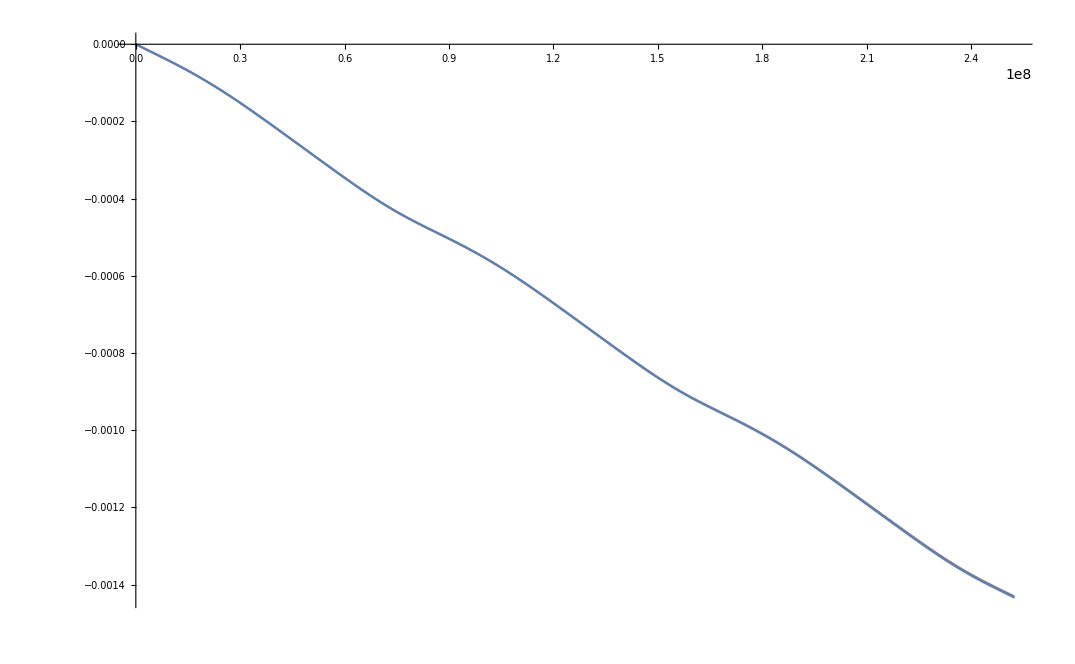

```mathematica
ϵ=10^-7;
δ=1;
P=5;
ω0=2*π/P;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=10/180.0*π;
k1=1;
k2=2;
ϵ1=(δ ϵ)/(1+δ+ϵ);
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First]
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);
χeff=ArcCos[Dot[e3eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]]
ηeff=ArcTan[Dot[e1eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}],Dot[e2eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]]
Spindown3[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=Ltol;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
N0=(k1 μ^2*ω0^2)/(c^3 I0);

l1=-N0*k2*t;
l2=N0*((μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m])/ωp+t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(δ μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)-(2 √(1+δ) μ1 μ2 JacobiDN[ϕ0+t ωp,m] Sin[θ0]^2)/(m ωp)-(√(1+δ) μ2 μ3 JacobiCN[ϕ0+t ωp,m] Sin[2 θ0])/ωp+(μ1 μ3 JacobiSN[ϕ0+t ωp,m] Sin[2 θ0])/ωp)+N0*(-1/(m ωp)(m μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0,m],m]-μ1^2 ϕ0 Sin[θ0]^2+m μ1^2 ϕ0 Sin[θ0]^2+μ2^2 ϕ0 Sin[θ0]^2+δ μ2^2 ϕ0 Sin[θ0]^2+μ1^2 EllipticE[JacobiAmplitude[ϕ0,m],m] Sin[θ0]^2-μ2^2 EllipticE[JacobiAmplitude[ϕ0,m],m] Sin[θ0]^2-δ μ2^2 EllipticE[JacobiAmplitude[ϕ0,m],m] Sin[θ0]^2-2 √(1+δ) μ1 μ2 JacobiDN[ϕ0,m] Sin[θ0]^2-m √(1+δ) μ2 μ3 JacobiCN[ϕ0,m] Sin[2 θ0]+m μ1 μ3 JacobiSN[ϕ0,m] Sin[2 θ0]));
l=l1+l2;
l

]
time=linearspace[0,8*yr,600];
sol=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[ϵ,δ,P,B,k,M,R,χ,η,θ,k1,k2]]]
re=(sol/.t-> time);
list1=ListPlot[Transpose@{time,(re[[1]]^2+re[[2]]^2+re[[3]]^2)^0.5-1},ColorFunction->"Rainbow",Joined->True];
list2=ListPlot[Transpose@{time,Spindown3[ϵeff,δeff,χeff,ηeff,θ0eff,B,P,k1,k2,time]},Joined->True];
Show[list1,list2,Background-> White]
```

## Special biaxial case

0.

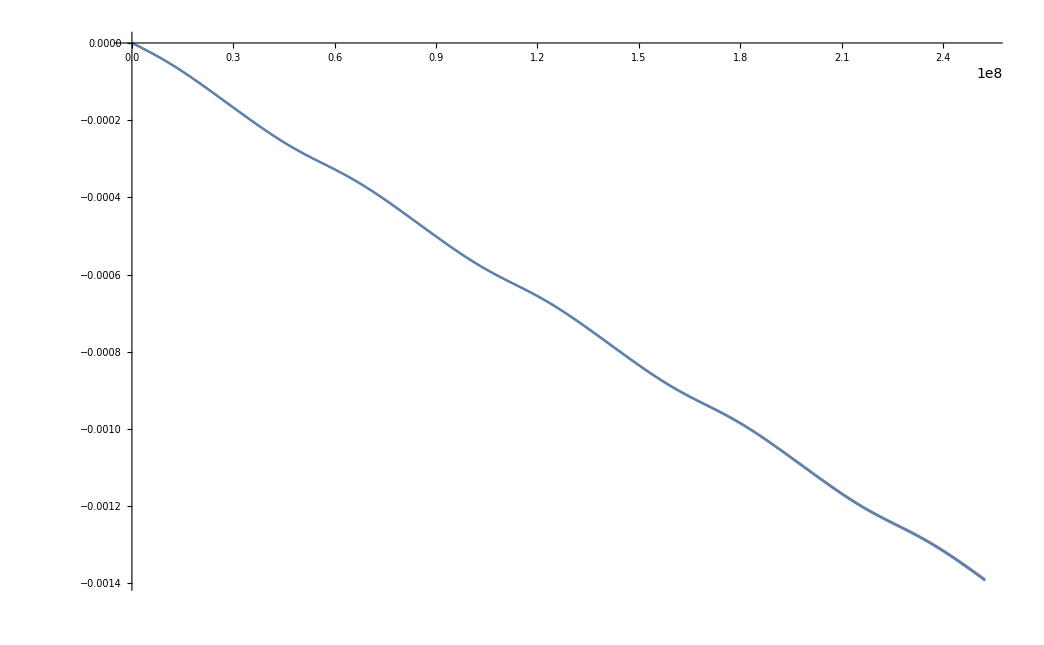

```mathematica
ϵ=10^-7;
δ=0;
P=5;
ω0=2*π/P;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=0.0/180*π;
θ=10/180.0*π;
k1=1;
k2=2;
ϵ1=(δ ϵ)/(1+δ+ϵ);
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q]
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);
χeff=ArcCos[Dot[e3eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]];
ηeff=ArcTan[Dot[e1eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}],Dot[e2eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]];
Spindown4[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,ϕ0_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=Ltol;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
(*L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];*)
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=-N0*k2*t;
τ=ωp*t;
l2=N0*((μ3^2 Cos[θ0]^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m])/ωp+t μ1^2 Sin[θ0]^2-(t μ1^2 Sin[θ0]^2)/m+(μ1^2 ϕ0 Sin[θ0]^2)/ωp-(μ1^2 ϕ0 Sin[θ0]^2)/(m ωp)+(μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(δ μ2^2 (ϕ0+t ωp-EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m]) Sin[θ0]^2)/(m ωp)+(μ1^2 EllipticE[JacobiAmplitude[ϕ0+t ωp,m],m] Sin[θ0]^2)/(m ωp)-(2 √(1+δ) μ1 μ2 JacobiDN[ϕ0+t ωp,m] Sin[θ0]^2)/(m ωp)-(√(1+δ) μ2 μ3 JacobiCN[ϕ0+t ωp,m] Sin[2 θ0])/ωp+(μ1 μ3 JacobiSN[ϕ0+t ωp,m] Sin[2 θ0])/ωp);
l=l1+l2;
l

]

sol=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[ϵ,δ,P,B,k,M,R,χ,η,θ,k1,k2]]];
time=linearspace[0,8*yr,600];

re=sol/.t-> time;
list1=ListPlot[Transpose@{time,(re[[1]]^2+re[[2]]^2+re[[3]]^2)^0.5-1},Joined->True,ColorFunction->Hue];
list2=ListPlot[Transpose@{time,Spindown4[ϵeff,δeff,χeff,ηeff,θ0eff,B,P,k1,k2,ϕ0,time]},Joined->True];
Show[list1,list2,Background-> White]
```

effectively, the star is triaxial and we need the triaxial solution to study the biaxial case

0.

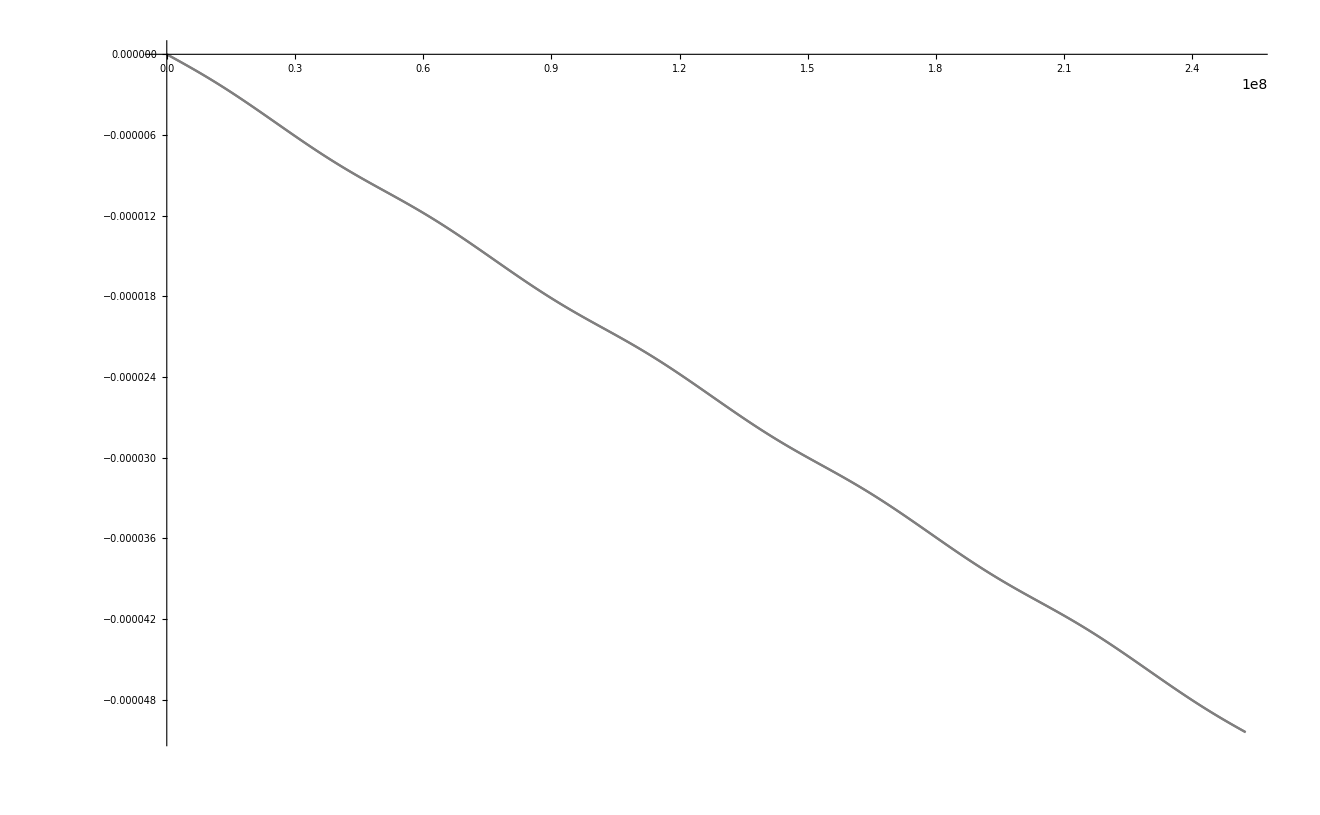

```mathematica
ϵ=10^-7;
δ=0;
P=5;
ω0=2*π/P;
B=10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=0.0/180*π;
θ=10/180.0*π;
k1=1;
k2=2;
ϵ1=(δ ϵ)/(1+δ+ϵ);
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q]
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);
χeff=ArcCos[Dot[e3eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]];
ηeff=ArcTan[Dot[e1eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}],Dot[e2eff,{Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]}]];
Spindown4[ϵ_,δ_,χ_,η_,θ0_,B_,P_,k1_,k2_,ϕ0_,t_]:=Module[{l},
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
M=1.4*Ms;
R=10*km;
ω0=2π/P;
μ=(B R^3)/2;
I0=2/5*M*R^2;
μ1=Sin[χ]Cos[η];
μ2=Sin[χ]Sin[η];
μ3=Cos[χ];
I1=I0;
I2=(I1 (1+δ) (1+ϵ))/(1+δ+ϵ);
I3=I1(1+ϵ);
L=Ltol;
ωp=ϵ*L*Cos[θ0]/(I3(1+δ)^0.5);
m=δ*Tan[θ0]^2;
T=(4 I3 Sqrt[1+δ]EllipticK[m])/(ϵ L *Cos[θ0]);
(*L1=Sin[θ0]*JacobiCN[ωp*t,m];
L2=Sin[θ0]*(1+δ)^0.5*JacobiSN[ωp*t,m];
L3=Cos[θ0]*JacobiDN[ωp*t,m];*)
N0=(k1 μ^2*ω0^2)/(c^3 I0);
l1=-N0*k2*t;
τ=ωp*t;
l2=N0/ωp*(1/4 (μ1^2 τ+2 μ3^2 τ-(μ1^2-2 μ3^2) τ Cos[2 θ0]+8 μ1 μ3 Cos[θ0] Sin[θ0] Sin[τ]+μ1^2 Sin[θ0]^2 Sin[2 τ]));
l=l1+l2;
l

]

sol=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[ϵ,δ,P,B,k,M,R,χ,η,θ,k1,k2]]];
time=linearspace[0,8*yr,600];

re=sol/.t-> time;
list1=ListPlot[Transpose@{time,(re[[1]]^2+re[[2]]^2+re[[3]]^2)^0.5-1},Joined->True,ColorFunction->Hue];
list2=ListPlot[Transpose@{time,Spindown4[ϵeff,δeff,χeff,ηeff,θ0eff,B,P,k1,k2,ϕ0,time]},Joined->True,ColorFunction->Hue];
Show[list1,list2,Background-> White]
```

```mathematica
time=linearspace[0,8*yr,600];
sol1=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,0,5,10^14,0.6,1.4*Ms,10*km,45/180*π,0,10/180*π,2/3,1]]];

s1=sol1/.t-> time;
s11=Flatten[(s1[[1]]^2+s1[[2]]^2+s1[[3]]^2)^0.5-1];
sol2=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,0,5,10^14,0.6,1.4*Ms,10*km,45/180*π,0,10/180*π,1,2]]];
s2=sol2/.t-> time;
s22=Flatten[(s2[[1]]^2+s2[[2]]^2+s2[[3]]^2)^0.5-1];
sol3=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,1,5,10^14,0.6,1.4*Ms,10*km,45/180*π,45/180*π,10/180*π,2/3,1]]];
s3=sol3/.t-> time;
s33=Flatten[(s3[[1]]^2+s3[[2]]^2+s3[[3]]^2)^0.5-1];
sol4=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,1,5,10^14,0.6,1.4*Ms,10*km,45/180*π,45/180*π,10/180*π,1,2]]];

s4=sol4/.t-> time;
s44=Flatten[(s4[[1]]^2+s4[[2]]^2+s4[[3]]^2)^0.5-1];
data=Transpose@{time,s11,s22,s33,s44};
SetDirectory[NotebookDirectory[]];
Export["./data/spindown1.dat",data];
```

```mathematica
sol1=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,0,5,5*10^14,0.6,1.4*Ms,10*km,45/180*π,0,10/180*π,2/3,1]]];

s1=sol1/.t-> time;
s11=Flatten[(s1[[1]]^2+s1[[2]]^2+s1[[3]]^2)^0.5-1];
sol2=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,0,5,5*10^14,0.6,1.4*Ms,10*km,45/180*π,0,10/180*π,1,2]]];
s2=sol2/.t-> time;
s22=Flatten[(s2[[1]]^2+s2[[2]]^2+s2[[3]]^2)^0.5-1];
sol3=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,1,5,5*10^14,0.6,1.4*Ms,10*km,45/180*π,45/180*π,10/180*π,2/3,1]]];
s3=sol3/.t-> time;
s33=Flatten[(s3[[1]]^2+s3[[2]]^2+s3[[3]]^2)^0.5-1];
sol4=Flatten[Evaluate[{u1[t],u2[t],u3[t]}/.farfield[10^-7,1,5,5*10^14,0.6,1.4*Ms,10*km,45/180*π,45/180*π,10/180*π,1,2]]];

s4=sol4/.t-> time;
s44=Flatten[(s4[[1]]^2+s4[[2]]^2+s4[[3]]^2)^0.5-1];
data=Transpose@{time,s11,s22,s33,s44};
SetDirectory[NotebookDirectory[]];
Export["./data/spindown2.dat",data];
```